# Thermodynamic quantities: Modified Condensate Ansatz

## Back-reaction equations (Euclidean Spacetime)

```mathematica
U[t_]=c1 JacobiSN[-I c1 t,-1]
```

-c1 JacobiSN[ⅈ c1 t,-1]

```mathematica
JacobiSN[-I t,-1]
```

-JacobiSN[ⅈ t,-1]

```mathematica
(*For Z(t)*)
```

```mathematica
DSolve[Z'[t]-D[U[t],t]/U[t] Z[t]+(2 √2 g)/U[t] JacobiSN[-I c1 t,-1]^2==0,Z,t]
```

{{Z→Function[{t},(2 √2 g t JacobiSN[ⅈ c1 t,-1])/c1+C[1] JacobiSN[ⅈ c1 t,-1]]}}

```mathematica
Z[t_]=(2 √2 g)/c1 t JacobiSN[I c1 t,-1]
```

(2 √2 g t JacobiSN[ⅈ c1 t,-1])/c1

## Deriving equations of motion for fluctuations

```mathematica
Clear[t,x,y,z]
```

```mathematica
coord={t,x,y,z};
n=4;(*# of spacetime dimensions*)
```

```mathematica
(*Euclidean*)
```

```mathematica
gdd={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
gUU= {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
(*Christoffel  symbols*)
```

```mathematica
ΓUdd=Table[1/2 Sum[gUU[[i]][[l]](D[gdd[[l]][[k]],coord[[j]]]+D[gdd[[l]][[j]],coord[[k]]]-D[ gdd[[j]][[k]],coord[[l]]]),{l,1,n}],{i,1,n},{j,1,n},{k,1,n}];
```

```mathematica
(*Gauge field A with 'a' as internal index and d as spacetime index= Aad*)
```

```mathematica
m=3;(*# of internal indices (SU(2))*)
```

```mathematica
Clear[U]
```

```mathematica
Aad={{0,U[t]+A11[t],A12[t],0},{0,A21[t],U[t]+A22[t],0},{0,0,0,U[t]+A33[t]}}
```

{{0,A11[t]+U[t],A12[t],0},{0,A21[t],A22[t]+U[t],0},{0,0,0,A33[t]+U[t]}}

```mathematica
MatrixForm[Aad]
```

(0 | A11[t]+U[t] | A12[t] | 0
0 | A21[t] | A22[t]+U[t] | 0
0 | 0 | 0 | A33[t]+U[t])

```mathematica
Clear[g]
```

```mathematica
Fadd=Table[D[Aad[[a]][[j]],coord[[i]]]- D[Aad[[a]][[i]],coord[[j]]] +Sum[LeviCivitaTensor[3] [[a,b,c]] Aad[[b]][[i]]Aad[[c]][[j]],{b,1,m},{c,1,m}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
FaUU=Table[Sum[gUU[[i]][[k]]gUU[[j]][[l]]Fadd[[a]][[k]][[l]],{k,1,n},{l,1,n}],{a,1,m},{i,1,n},{j,1,n}];
```

```mathematica
Sum[FaUU[[a]][[i]][[j]]Fadd[[a]][[i]][[j]],{a,1,m},{i,1,n},{j,1,n}]
```

2 A12[t]^2 (A33[t]+U[t])^2+2 A21[t]^2 (A33[t]+U[t])^2+2 (A11[t]+U[t])^2 (A33[t]+U[t])^2+2 (A22[t]+U[t])^2 (A33[t]+U[t])^2+(A12[t] A21[t]-(A11[t]+U[t]) (A22[t]+U[t]))^2+(-A12[t] A21[t]+(A11[t]+U[t]) (A22[t]+U[t]))^2+2 A12'[t]^2+2 A21'[t]^2+(-A11'[t]-U'[t])^2+(-A22'[t]-U'[t])^2+(-A33'[t]-U'[t])^2+(A11'[t]+U'[t])^2+(A22'[t]+U'[t])^2+(A33'[t]+U'[t])^2

```mathematica
Clear[U]
```

```mathematica
%217//Simplify
```

2 (A12[t]^2 (A33[t]+U[t])^2+A21[t]^2 (A33[t]+U[t])^2+(A11[t]+U[t])^2 (A33[t]+U[t])^2+(A22[t]+U[t])^2 (A33[t]+U[t])^2+(A12[t] A21[t]-(A11[t]+U[t]) (A22[t]+U[t]))^2+A12'[t]^2+A21'[t]^2+(A11'[t]+U'[t])^2+(A22'[t]+U'[t])^2+(A33'[t]+U'[t])^2)

```mathematica
(*∇_μ F^μν*)
CovDFaUU=Table[Sum[D[FaUU[[a]][[k]][[j]],coord[[k]]] +
Sum[ ΓUdd[[k]][[k]][[l]] FaUU[[a]][[l]][[j]] + ΓUdd[[j]][[k]][[l]]FaUU[[a]][[k]][[l]],{l,1,n}] ,{k,1,n}],{a,1,m},{j,1,n}];
(*g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
NonaU=Table[Sum[LeviCivitaTensor[3] [[a,b,c]] Aad[[b]][[i]] FaUU[[c]][[i]][[j]],{b,1,m},{c,1,m},{i,1,n}],{a,1,m},{j,1,n}];
(*∇_μ F^μν+g Subscript[f, abc] Subscript[A, μ]^b F^cμν*)
YMeq=CovDFaUU+NonaU;
```

```mathematica
YMeq[[1]]//MatrixForm
```

(0
-((A11[t]+U[t]) (A33[t]+U[t])^2)+(A22[t]+U[t]) (A12[t] A21[t]-(A11[t]+U[t]) (A22[t]+U[t]))+A11''[t]+U''[t]
-A12[t] (A33[t]+U[t])^2+A21[t] (-A12[t] A21[t]+(A11[t]+U[t]) (A22[t]+U[t]))+A12''[t]
0)

## Evaluating Thermodynamic potential

### Numerically solving equations of motion

```mathematica
Clear[c1,g]
```

```mathematica
Z[t_]=(2 √2 g)/c1 t JacobiSN[I c1 t,-1]
```

(2 √2 g t JacobiSN[ⅈ c1 t,-1])/c1

```mathematica
U[t_]=c1 JacobiSN[-I c1 t,-1]
```

-c1 JacobiSN[ⅈ c1 t,-1]

```mathematica
c1=300;g=0.6;
```

```mathematica
U[t]
```

-300 JacobiSN[300 ⅈ t,-1]

```mathematica
Z[t]
```

0.00565685 t JacobiSN[300 ⅈ t,-1]

```mathematica
(*Trying to solve analytically for Subscript[(Ã)^1, 2]*)
```

```mathematica
DSolve[y''[t]+U[t]^2 Z[t]+I g 2 √2 JacobiCN[-I c1 t,-1]JacobiDN[-I c1 t,-1]==0,y,t]
```

{{y→Function[{t},-(ⅈ √2 g ArcTan[JacobiCD[ⅈ c1 t,-1]])/c1^2+C[1]+t C[2]+(ⅈ √2 g (ArcTan[JacobiCD[ⅈ c1 t,-1]]+ⅈ c1 t JacobiSN[ⅈ c1 t,-1]))/c1^2]}}

```mathematica
-(ⅈ √2 g ArcTan[JacobiCD[ⅈ c1 t,-1]])/c1^2+C[1]+t C[2]+(ⅈ √2 g (ArcTan[JacobiCD[ⅈ c1 t,-1]]+ⅈ c1 t JacobiSN[ⅈ c1 t,-1]))/c1^2//Simplify
```

C[1]+t C[2]-(√2 g t JacobiSN[ⅈ c1 t,-1])/c1

```mathematica
D[JacobiSN[t,-1],t]
```

JacobiCN[t,-1] JacobiDN[t,-1]

```mathematica
(* Subscript[(Ã)^1, 2] *)
```

```mathematica
y1=NDSolve[{y''[t]+U[t]^2 Z[t]+I g 2 √2 JacobiCN[-I c1 t,-1]JacobiDN[-I c1 t,-1]==0,y[0]==0,y'[0]==0},y[t],{t,0,10}]
```

{{y[t]→InterpolatingFunction[{{0., 10.}}, <>][t]}}

```mathematica
A12[t_]=y[t]/.y1
```

{InterpolatingFunction[{{0., 10.}}, <>][t]}

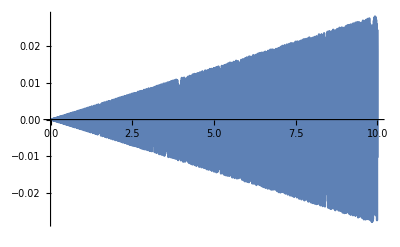

```mathematica
Plot[Im[A12[t]],{t,0,10}]
```

```mathematica
(*Subscript[(Ã)^1, 2]*)
```

```mathematica
A21[t_]=A12[t]+Z[t];
```

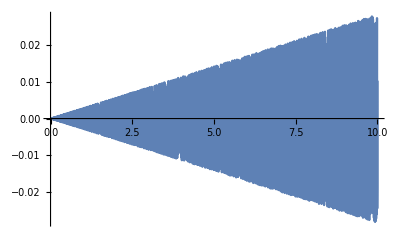

```mathematica
Plot[Im[A21[t]],{t,0,10}]
```

```mathematica
(* Subscript[(Ã)^1, 1],Subscript[(Ã)^3, 2],Subscript[(Ã)^3, 3]*)
```

```mathematica
sol=NDSolve[{y''[t]-6 U[t]^2 y[t]+I 11/(√2)g==0,z''[t]+I 3/(√2)g-2 U[t]^2 y[t]==0,w''[t]+I 5/(√2)g-2 U[t]^2 y[t]==0,w[0]==0,w'[0]==0,y[0]==0,y'[0]==0,z[0]==0,z'[0]==0},{y,z,w},{t,0,10}]
```

{{y→InterpolatingFunction[{{0., 10.}}, <>],z→InterpolatingFunction[{{0., 10.}}, <>],w→InterpolatingFunction[{{0., 10.}}, <>]}}

```mathematica
A11[t_]=z[t]/.sol
```

{InterpolatingFunction[{{0., 10.}}, <>][t]}

```mathematica
A22[t_]=z[t]/.sol
```

{InterpolatingFunction[{{0., 10.}}, <>][t]}

```mathematica
A33[t_]=w[t]/.sol
```

{InterpolatingFunction[{{0., 10.}}, <>][t]}

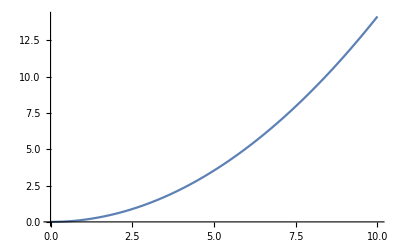

```mathematica
Plot[Im[A11[t]],{t,0,10}]
```

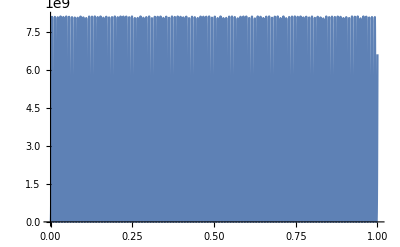

```mathematica
Plot[U[t]^4,{t,0,1}]
```

```mathematica
(*F^2*)
```

```mathematica
F2[t_]=2 A12[t]^2 (A33[t]+U[t])^2+2 A21[t]^2 (A33[t]+U[t])^2+2 (A11[t]+U[t])^2 (A33[t]+U[t])^2+2 (A22[t]+U[t])^2 (A33[t]+U[t])^2+(A12[t] A21[t]-(A11[t]+U[t]) (A22[t]+U[t]))^2+(-A12[t] A21[t]+(A11[t]+U[t]) (A22[t]+U[t]))^2+2 A12'[t]^2+2 A21'[t]^2+(-A11'[t]-U'[t])^2+(-A22'[t]-U'[t])^2+(-A33'[t]-U'[t])^2+(A11'[t]+U'[t])^2+(A22'[t]+U'[t])^2+(A33'[t]+U'[t])^2;
```

```mathematica
Clear[F2int]
```

```mathematica
F2int[T_?NumberQ]:=NIntegrate[F2[t],{t,0,1/T}]
```

### Thermodynamic potential for Modified Ansatz

```mathematica
Λms=176;Λ=2π T;Nc=2;Nf=2;β0=1/(4π)^2(11/3 Nc-2/3 Nf);
α[T_]=2Log[Λ/Λms];Pideal=π^2/45 T^4(Nc^2-1)+(7 π^2)/180 T^4 Nc Nf;
αs[T_]=1/(4π β0 α[T])(1);(*For only loop *)
Press1m[T_]= -(-1/45 (-1+Nc^2) π^2 (T)^4-7/180 Nc Nf π^2 (T)^4-1/(48 π^2)c1^3 (-Nc+Nf) (0)+T F2int[T] (-(1/(4 (4π) αs[T]))-(Nf Log[4])/(48 π^2)+1/2 β0 Log[Λ/(4 π T)]))/Pideal;
Thdpot1m[T_]= (-1/45 (-1+Nc^2) π^2 (T)^4-7/180 Nc Nf π^2 (T)^4-1/(48 π^2)c1^3 (-Nc+Nf) (0)+T F2int[T] (-(1/(4 (4π) αs[T]))-(Nf Log[4])/(48 π^2)+1/2 β0 Log[Λ/(4 π T)]))/Pideal;
```

```mathematica
data=Table[First[Re[Evaluate[Press1m[T]]]],{T,125,500,5}]
```

{-0.169956,0.0914644,0.297947,0.459648,0.584545,0.679172,0.74905,0.798934,0.832939,0.854607,0.866954,0.872498,0.8733,0.871007,0.866898,0.861941,0.856837,0.852076,0.847973,0.844718,0.842397,0.841027,0.840578,0.840985,0.842164,0.844023,0.846466,0.849398,0.852732,0.856386,0.860286,0.864367,0.868571,0.87285,0.87716,0.881468,0.885744,0.889963,0.894107,0.898159,0.902109,0.905946,0.909665,0.913261,0.916732,0.920076,0.923293,0.926386,0.929354,0.932201,0.93493,0.937544,0.940046,0.942441,0.944731,0.946921,0.949015,0.951017,0.95293,0.954759,0.956506,0.958176,0.959773,0.961298,0.962757,0.964151,0.965484,0.966758,0.967977,0.969144,0.970259,0.971327,0.972349,0.973328,0.974265,0.975162}

```mathematica
temp=Table[i,{i,125,500,5}]
```

{125,130,135,140,145,150,155,160,165,170,175,180,185,190,195,200,205,210,215,220,225,230,235,240,245,250,255,260,265,270,275,280,285,290,295,300,305,310,315,320,325,330,335,340,345,350,355,360,365,370,375,380,385,390,395,400,405,410,415,420,425,430,435,440,445,450,455,460,465,470,475,480,485,490,495,500}

```mathematica
Length[temp]
```

76

```mathematica
Press1mval=Table[{temp[[i]],data[[i]]},{i,1,76}]
```

{{125,-0.169956},{130,0.0914644},{135,0.297947},{140,0.459648},{145,0.584545},{150,0.679172},{155,0.74905},{160,0.798934},{165,0.832939},{170,0.854607},{175,0.866954},{180,0.872498},{185,0.8733},{190,0.871007},{195,0.866898},{200,0.861941},{205,0.856837},{210,0.852076},{215,0.847973},{220,0.844718},{225,0.842397},{230,0.841027},{235,0.840578},{240,0.840985},{245,0.842164},{250,0.844023},{255,0.846466},{260,0.849398},{265,0.852732},{270,0.856386},{275,0.860286},{280,0.864367},{285,0.868571},{290,0.87285},{295,0.87716},{300,0.881468},{305,0.885744},{310,0.889963},{315,0.894107},{320,0.898159},{325,0.902109},{330,0.905946},{335,0.909665},{340,0.913261},{345,0.916732},{350,0.920076},{355,0.923293},{360,0.926386},{365,0.929354},{370,0.932201},{375,0.93493},{380,0.937544},{385,0.940046},{390,0.942441},{395,0.944731},{400,0.946921},{405,0.949015},{410,0.951017},{415,0.95293},{420,0.954759},{425,0.956506},{430,0.958176},{435,0.959773},{440,0.961298},{445,0.962757},{450,0.964151},{455,0.965484},{460,0.966758},{465,0.967977},{470,0.969144},{475,0.970259},{480,0.971327},{485,0.972349},{490,0.973328},{495,0.974265},{500,0.975162}}

```mathematica
Press1mval={{125,-0.16995616931409827},{130,0.09146437504591844},{135,0.2979471464768428},{140,0.4596476926131753},{145,0.5845447935950203},{150,0.6791715237274721},{155,0.74904992438403},{160,0.7989340099432231},{165,0.8329386108758795},{170,0.8546074173427018},{175,0.8669543906509629},{180,0.8724983300878466},{185,0.8733002569466348},{190,0.8710067103929953},{195,0.866898276684683},{200,0.8619409256169792},{205,0.8568373082276831},{210,0.8520755078073148},{215,0.8479734139558863},{220,0.8447176340014012},{225,0.8423965143821195},{230,0.8410273501240498},{235,0.8405782021807023},{240,0.840984939200985},{245,0.8421642038631482},{250,0.8440230075444505},{255,0.8464656100421681},{260,0.8493982663066619},{265,0.8527323362205464},{270,0.8563861672737964},{275,0.860286080054438},{280,0.8643667161216264},{285,0.8685709482282686},{290,0.872849503853428},{295,0.8771604136812924},{300,0.8814683657653798},{305,0.8857440222913915},{310,0.8899633378025342},{315,0.8941069043135139},{320,0.8981593389152335},{325,0.902108722432119},{330,0.9059460927659571},{335,0.9096649932106277},{340,0.9132610738346517},{345,0.91673174268274},{350,0.9200758628004527},{355,0.9232934907556588},{360,0.9263856522820977},{365,0.9293541508057646},{370,0.9322014048634882},{375,0.9349303107349791},{380,0.9375441269502536},{385,0.9400463776803422},{390,0.9424407723554074},{395,0.9447311391714682},{400,0.9469213704396573},{405,0.9490153779978372},{410,0.9510170571430471},{415,0.9529302577552836},{420,0.9547587614700942},{425,0.9565062639212316},{430,0.95817636121733},{435,0.959772539940345},{440,0.9612981700604722},{445,0.9627565002543774},{450,0.9641506551926873},{455,0.9654836344304675},{460,0.9667583125923292},{465,0.967977440593221},{470,0.9691436476780155},{475,0.9702594440987458},{480,0.9713272242786748},{485,0.9723492703380635},{490,0.9733277558782287},{495,0.9742647499388069},{500,0.9751622210586163}};
```

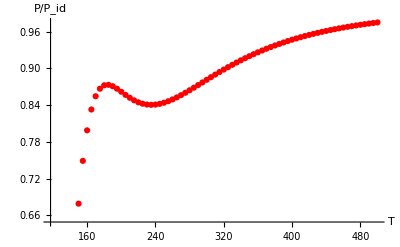

```mathematica
p1=ListPlot[Press1mval,PlotStyle->Red,AxesLabel->{"T","P/P_id"}]
```

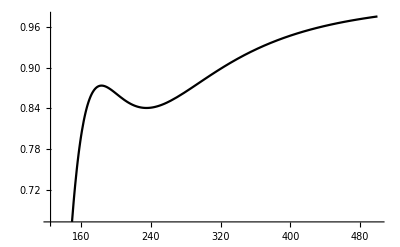

```mathematica
p2=Plot[Press1[300,0,T],{T,125,500},PlotStyle->Black]
```

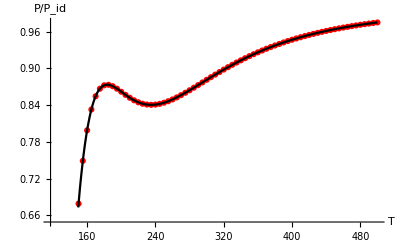

```mathematica
Show[p1,p2]
```

```mathematica
Plot[Evaluate[Press[T]],{T,100,500}]
```

$Aborted